## Results

```mathematica
SetDirectory[NotebookDirectory[] <> "/results"];
```

## N(τ_0)

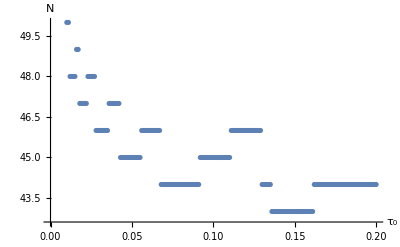

```mathematica
data:=Import["initstep_n.dat"]
ListPlot[data, AxesLabel->{"τ_0", "N"}]
```

## N(fac)

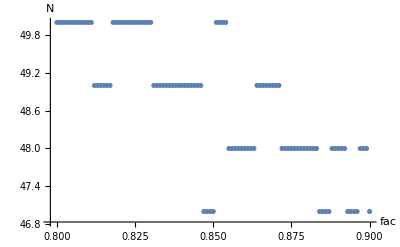

```mathematica
data:=Import["fac_n.dat"]
ListPlot[data, AxesLabel->{"fac", "N"}]
```

## N(facmax)

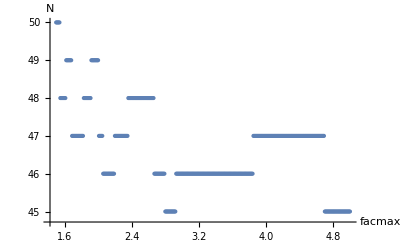

```mathematica
data:=Import["facmax_n.dat"]
ListPlot[data,AxesLabel->{"facmax", "N"}]
```

## N(facmin)

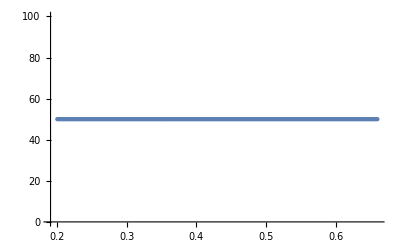

```mathematica
data:=Import["facmin_n.dat"]
ListPlot[data]
```

## N_rej(τ_0)

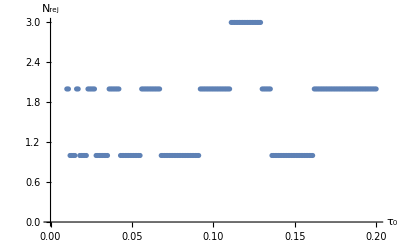

```mathematica
data:=Import["initstep_nrej.dat"]
ListPlot[data,AxesLabel->{"τ_0","N_rej"}]
```

## N_rej(fac)

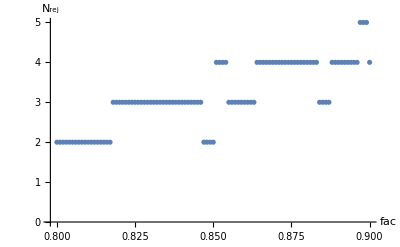

```mathematica
data:=Import["fac_nrej.dat"]
ListPlot[data,AxesLabel->{"fac","N_rej"}]
```

## N_rej(facmax)

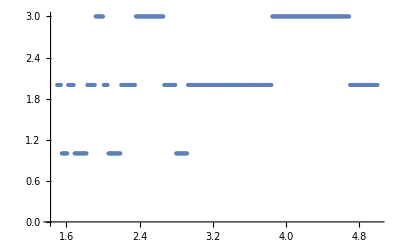

```mathematica
data:=Import["facmax_nrej.dat"]
ListPlot[data]
```

## N_rej(facmin)

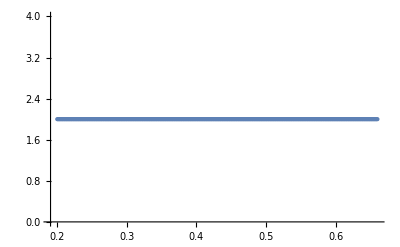

```mathematica
data:=Import["facmin_nrej.dat"]
ListPlot[data]
```

## T(τ_0)

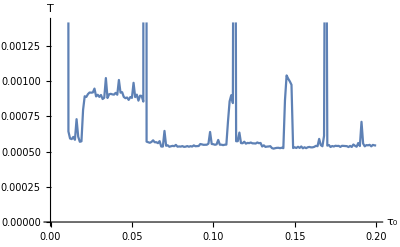

```mathematica
data:=Import["initstep_time.dat"]
ListLinePlot[data,AxesLabel->{"τ_0", "T"}]
```

## T(fac)

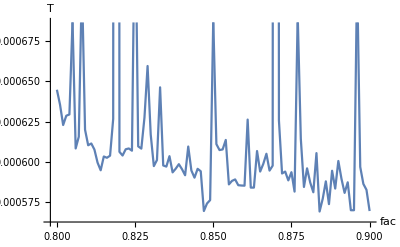

```mathematica
data:=Import["fac_time.dat"]
ListLinePlot[data,AxesLabel->{"fac", "T"}]
```

## T(facmax)

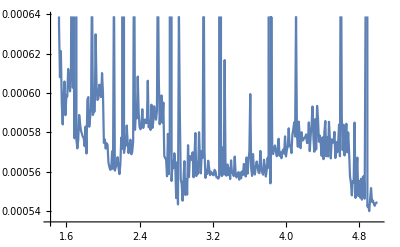

```mathematica
data:=Import["facmax_time.dat"]
ListLinePlot[data]
```

## T(facmin)

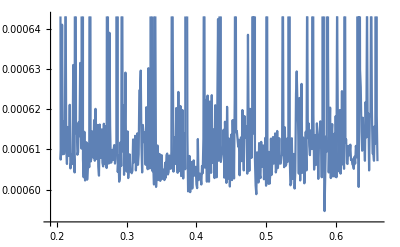

```mathematica
data:=Import["facmin_time.dat"]
ListLinePlot[data]
```

## ϵ(τ_0)

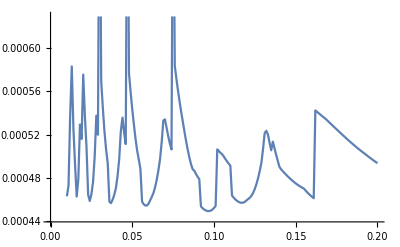

```mathematica
data:=Import["initstep_err.dat"]
ListLinePlot[data]
```

## ϵ(fac)

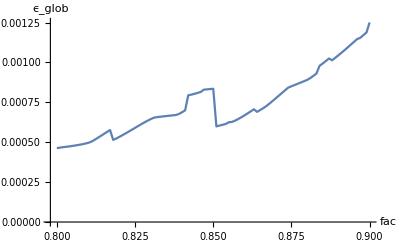

```mathematica
data:=Import["fac_err.dat"]
ListLinePlot[data,AxesLabel->{"fac","ϵ_glob"}]
```

## ϵ(facmax)

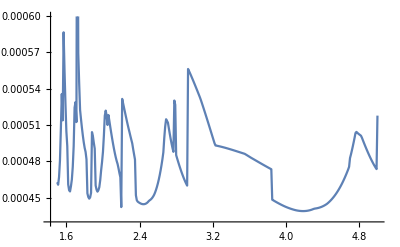

```mathematica
data:=Import["facmax_err.dat"]
ListLinePlot[data]
```

## ϵ(facmin)

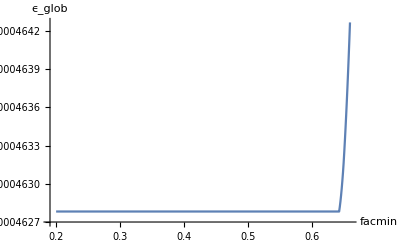

```mathematica
data:=Import["facmin_err.dat"]
ListLinePlot[data,AxesLabel->{"facmin","ϵ_glob"}]
```

## Algorithm monitoring

Ensure that files in “monitoring” contain information about method you want (since it have same names both for Runge - Kutta and Dormand - Prince methods.

```mathematica
SetDirectory[NotebookDirectory[] <> "/monitoring"];
```

## Runge - Kutta

### Global error

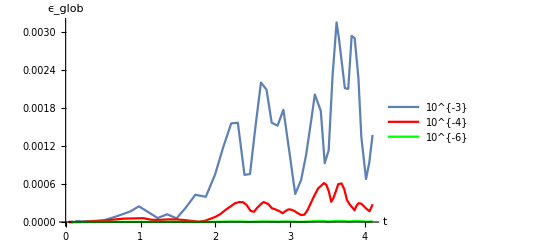

```mathematica
data3:= Import["global_err_rk_1.00e-03.dat"]
data4:= Import["global_err_rk_1.00e-04.dat"]
data6:= Import["global_err_rk_1.00e-06.dat"]
g3=ListLinePlot[data3,PlotLegends->Placed[{"10^{-3}"},Right]];
g4=ListLinePlot[data4,PlotStyle->Red,PlotLegends->Placed[{"10^{-4}"},Right]];
g6=ListLinePlot[data6,PlotStyle->Green,PlotLegends->Placed[{"10^{-6}"},Right]];
Show[g3,g4,g6,AxesLabel->{"t","ϵ_glob"}]
```

### Local error

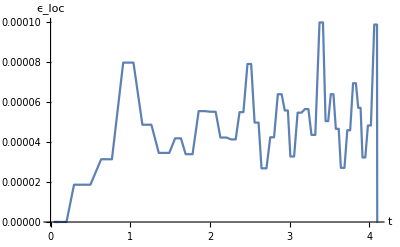

```mathematica
data:= Import["local_err.dat"]
ListLinePlot[data,AxesLabel->{"t","ϵ_loc"}]
```

### Steps

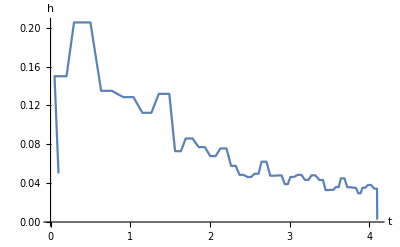

```mathematica
data:= Import["steps.dat"]
ListLinePlot[data,AxesLabel->{"t", "h"}]
```

### Values

```mathematica
data:= Import["vals.dat"]
y1={};
y2={};
For[i=1,i<Length[data],i++,
AppendTo[y1, {data⟦i⟧⟦1⟧, data⟦i⟧⟦2⟧}];
AppendTo[y2, {data⟦i⟧⟦1⟧, data⟦i⟧⟦3⟧}];
]
g1=ListLinePlot[y1,PlotStyle->Red,PlotLegends->Placed[{"y_1"},Right]];
g2=ListLinePlot[y2,PlotLegends->Placed[{"y_2"},Right]];
```

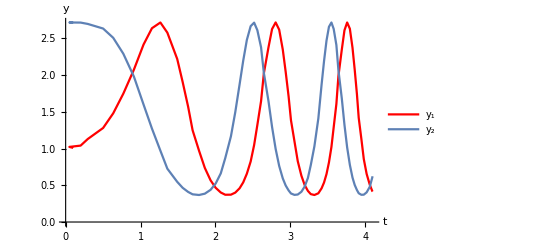

```mathematica
g3=Show[g1,g2,AxesLabel->{"t", "y"}]
```

## Dormand - Prince

### Global error

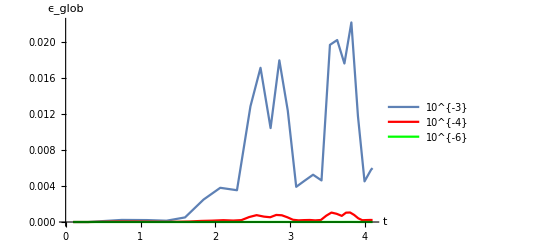

```mathematica
data3:= Import["global_err_dp_1.00e-03.dat"]
data4:= Import["global_err_dp_1.00e-04.dat"]
data6:= Import["global_err_dp_1.00e-06.dat"]
g3=ListLinePlot[data3,PlotLegends->Placed[{"10^{-3}"},Right]];
g4=ListLinePlot[data4,PlotStyle->Red,PlotLegends->Placed[{"10^{-4}"},Right]];
g6=ListLinePlot[data6,PlotStyle->Green,PlotLegends->Placed[{"10^{-6}"},Right]];
Show[g3,g4,g6,AxesLabel->{"t","ϵ_glob"}]
```

#### Local error

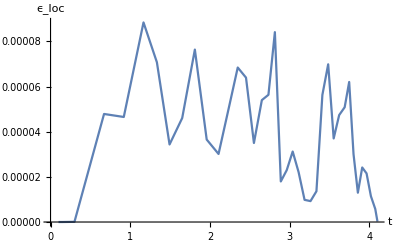

```mathematica
data:= Import["local_err.dat"]
ListLinePlot[data,AxesLabel->{"t","ϵ_loc"}]
```

### Steps

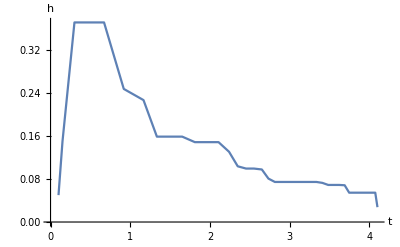

```mathematica
data:= Import["steps.dat"]
ListLinePlot[data,AxesLabel->{"t", "h"}]
```

#### Values

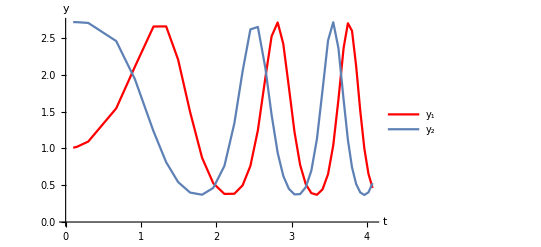

```mathematica
data:= Import["vals.dat"]
y1={};
y2={};
For[i=1,i<Length[data],i++,
AppendTo[y1, {data⟦i⟧⟦1⟧, data⟦i⟧⟦2⟧}];
AppendTo[y2, {data⟦i⟧⟦1⟧, data⟦i⟧⟦3⟧}];
]
g1=ListLinePlot[y1,PlotStyle->Red,PlotLegends->Placed[{"y_1"},Right]];
g2=ListLinePlot[y2,PlotLegends->Placed[{"y_2"},Right]];
Show[g1,g2,AxesLabel->{"t", "y"}]
```